# Math 385 HW # 8

## Mario L Gutierrez Abed

For P_i we’re going to pick any 25 equidistantly spaced points on f(x)=1/(1+x^2) on the interval [-5,5] (**they have to be ON the function!**). 

(1) Set up σ^j(t). Then
-Loop over the number of points - 3 (i.e. 25-3=22)
-Plot σ^j(t) and f(x) on the same plot.

Solution:
I’m going to create a list of  the 25 points that I’m going to work with. 
First, I will split it into two lists: one with the x-coordinates and the other one with the y-coordinates :

```mathematica
f[x_]=1/(1+x^2);

xcoords=Table[i,{i,-5,5,.41}]
ycoords=Table[f[i],{i,-5,5,.41}]
Length[xcoords]
Length[ycoords]
```

{-5.,-4.59,-4.18,-3.77,-3.36,-2.95,-2.54,-2.13,-1.72,-1.31,-0.9,-0.49,-0.08,0.33,0.74,1.15,1.56,1.97,2.38,2.79,3.2,3.61,4.02,4.43,4.84}

{0.0384615,0.0453143,0.0541348,0.0657337,0.0813696,0.103066,0.134199,0.180606,0.252627,0.368175,0.552486,0.806387,0.993641,0.901795,0.646162,0.430571,0.29124,0.20488,0.150051,0.113842,0.088968,0.0712652,0.0582737,0.0484851,0.0409407}

25

25

Now we put the x’s and corresponding y’s together in a new list and we show that these points are on the graph of f(x):

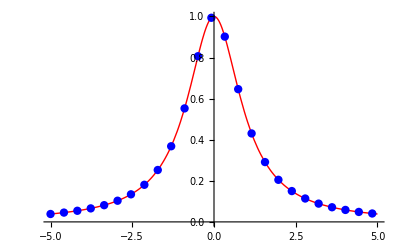

```mathematica
pts={};
For[j=1,j≤25,j++,
AppendTo[pts,{xcoords⟦j⟧,ycoords⟦j⟧}]
]
functionplot=Plot[f[x],{x,-5,5},PlotStyle->Red];
pointsplot=ListPlot[pts,PlotStyle->{Blue,PointSize[0.015]}];
Show[functionplot,pointsplot]
```

Sweet. Now let’s set up our spline segments σ^j(t) : 
Given a list of points P_i=(x_i,y_i), for i=1,...,n, we have that 

σ^j(t)=∑ _(i=1)^4 p_i(t)P_(j+i-1)
=1/6[ (-t^3+3 t^2-3t+1)P_j+(3 t^3-6 t^2+4)P_(j+1)+(-3 t^3+3 t^2+3t+1)P_(j+2)+t^3 P_(j+3)]

where t∈[0,1] and j≤n-3. 
Now let’s get on with the computations:

```mathematica
segments={};
For[j=1,j≤Length[pts]-3,j++,
σ=1/6*(-t^3+3 t^2-3t+1)*pts⟦j⟧+1/6*(3 t^3-6 t^2+4)*pts⟦j+1⟧+1/6*(-3 t^3+3 t^2+3t+1)*pts⟦j+2⟧+1/6*t^3*pts⟦j+3⟧;
AppendTo[segments,σ];
];
awesomeness=ParametricPlot[segments,{t,0,1},AspectRatio->Full]
```

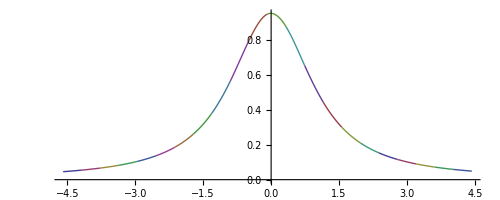

Awesome, now let’s plot f(x) and our spline segments together on the same plot :

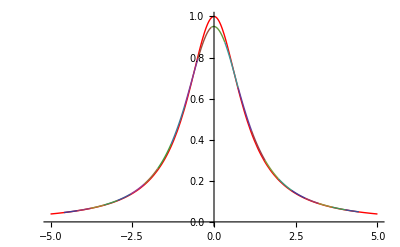

```mathematica
Show[functionplot,awesomeness]
```

Good stuff! 
We could’ve also used Mathematica’s default Splines package to plot our spline segments...

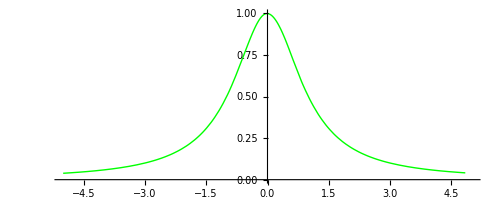

```mathematica
<<Splines`
ζ=SplineFit[pts,Cubic];
μ=ParametricPlot[ζ[t],{t,0,24},PlotStyle->Green,PlotRange->{{-5,5},{0,1}},AspectRatio->Full]
```

Or we could’ve used the B spline built-in function...

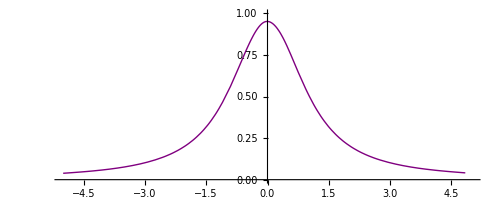

```mathematica
ω=BSplineFunction[pts];
κ=ParametricPlot[ω[t],{t,0,1},PlotStyle->Purple,PlotRange->{{-5,5},{0,1}},AspectRatio->Full]
```

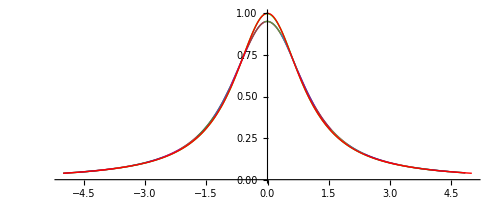

```mathematica
Show[μ,κ,awesomeness,functionplot]
```

Enough plotting, let’s move on to part 2...

(2) In which segment is (3/4,*)? What is *?

```mathematica
r[t_]=segments;
times={};
For[i=1,i≤Length[r[t]],i++,
ψ=FindRoot[r[t]⟦i,1⟧==3/4,{t,0,1}]⟦1,2⟧;
AppendTo[times,ψ]
];
For[j=1,j≤Length[times],j++,
If[0≤times⟦j⟧≤1,
Subscript[t, 0]=times⟦j⟧;
Print["t_0= ",times⟦j⟧];
Print["t_0 is found on segment ",j]
];
]
```

t_0= 0.0243902

t_0 is found on segment 14

Now that we’ve found the segment where (3/4,*) is located, we can easily determine what * is...

```mathematica
r[Subscript[t, 0]]⟦14⟧
```

{0.75,0.647101}

Hence,  * is

```mathematica
Print["* = ",r[Subscript[t, 0]]⟦14,2⟧]
```

* = 0.647101